# LEP Bound on Scalar

```mathematica
Quit[]
```

## SM Parameters

```mathematica
mb=4.19;
mc=1.27;
mτ=1.78;
```

## Branching Ratio

```mathematica
bBR[mS_]:=(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
cBR[mS_]:=(3 mc^2 Re[(mS^2-4 mc^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);τBR[mS_]:=(mτ^2 Re[(mS^2-4 mτ^2)^(3/2)])/(3 mb^2 Re[(mS^2-4 mb^2)^(3/2)]+3 mc^2 Re[(mS^2-4 mc^2)^(3/2)]+mτ^2 Re[(mS^2-4 mτ^2)^(3/2)]);
```

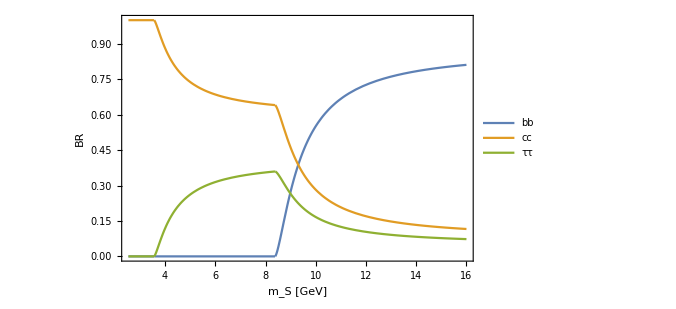

```mathematica
Plot[{bBR[mS],cBR[mS],τBR[mS]},{mS,2mc,16},PlotLegends->Placed[LineLegend[{Style["bb",FontFamily->"Times",FontSize->16],Style["cc",FontFamily->"Times",FontSize->16],Style["ττ",FontFamily->"Times",FontSize->16]},Spacings->0.15,LegendMarkerSize->30,LegendFunction->(Framed[#1, FrameMargins -> 0,RoundingRadius->5] & ),LegendLayout->"Row"],{0.75,0.88}],BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->16],Style["BR",FontFamily->"Times",FontSize->16]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->16]}]
```

## LEP bound

```mathematica
bb‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"bb.csv"]][mS];
ττ‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"tautau.csv"]][mS];
independent‵limit[mS_]:=Interpolation[Import[NotebookDirectory[]<>"independent.csv"]][mS];
```

```mathematica
bb‵bound[mS_/;mS≥12.4]=√((bb‵limit[mS])/bBR[mS]);
bb‵bound[mS_/;mS<12.4]=1;
ττ‵bound[mS_/;mS≥3.9]=√((ττ‵limit[mS])/τBR[mS]);
ττ‵bound[mS_/;mS<3.9]=1;
```

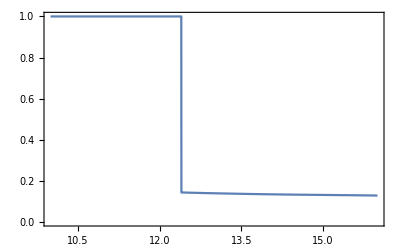

```mathematica
Plot[bb‵bound[mS],{mS,10,16}]
```

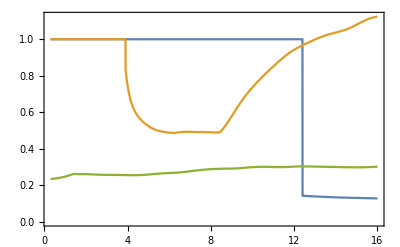

```mathematica
Plot[{bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])},{mS,0.3,16}]
```

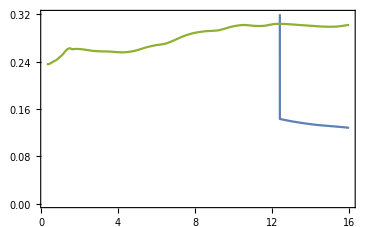

```mathematica
Plot[{bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])},{mS,0.3,16},PlotRange->{{0.3,16},{0,0.32}}]
```

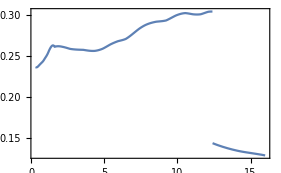

```mathematica
Plot[Min[bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])],{mS,0.3,16}]
```

```mathematica
boundlist=Table[{mS,Min[bb‵bound[mS],ττ‵bound[mS],√(independent‵limit[mS])]},{mS,0.3,16.,0.1}];
```

InterpolatingFunction::dmval: Input value {3.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/output/LEPbound.csv",boundlist];
```